# 蜻蜓算法

```mathematica
fitness[xn_]:=20+Sum[x^2-10Cos[2π x],{x,xn}]
Plot3D[fitness[{x,y}],{x,-5,5},{y,-5,5},ColorFunction->Hue,Mesh->None,RotationAction->"Clip"]
```

-Graphics3D-

```mathematica
fitness[{0,0}]
```

0

## DA 实现

```mathematica
levy[d_]:=Block[{β=3/2,σ},σ=((Gamma[1+β]Sin[π β/2])/(Gamma[(1+β)/2]β 2^((β-1)/2)))^(1/β);
0.01(RandomVariate[NormalDistribution[],d]σ)/Abs[RandomVariate[NormalDistribution[],d]]^(1/β)]
```

```mathematica
levy[2]
```

{-0.00374963,0.00218879}

```mathematica
0.01RandomVariate[LevyDistribution[-1,1.5],{1,2}]
```

{{1.98068,0.304878}}

```mathematica
ub=5;
lb=-5;
dimension=2;
num=50;

x=RandomReal[{ub,lb},{num,dimension}];
deltaX=RandomReal[{ub,lb},{num,dimension}];
xFood=RandomReal[{ub,lb},dimension];
fitFood=∞;
xEnemy=RandomReal[{ub,lb},dimension];
fitEnemy=-∞;

iterNum=100;
fitCurve=Table[0,iterNum];
(*迭代*)
Monitor[Do[
r=(ub-lb)/4+(ub-lb)(2iter)/iterNum;
w=0.9-iter (0.9-0.4)/iterNum;
e=0.1-iter (0.1 2)/iterNum;
If[e<0,e=0];
s=2RandomReal[] e;
a=2RandomReal[] e;
c=2RandomReal[]e;
f=2RandomReal[];

(*计算目标函数*)
Do[fit=fitness[x[[i]]];
If[fit<fitFood,fitFood=fit;xFood=x[[i]]];
If[fit>fitEnemy,fitEnemy=fit;xEnemy=x[[i]]],{i,num}];
fitCurve[[iter]]=fitFood;

(*遍历所有个体*)
Do[
neighboursNo=0;
neighboursX={};
neighboursDeltaX={};
(*寻找邻居*)
Do[
If[EuclideanDistance[x[[u]],x[[v]]]<=r,neighboursNo++;AppendTo[neighboursX,x[[v]]];
AppendTo[neighboursDeltaX,deltaX[[v]]];
],{v,num}];

If[neighboursNo>0,
Si=-Sum[x[[u]]-j,{j,neighboursX}];
Ai=Mean[neighboursDeltaX];
Ci=Mean[neighboursX]-x[[u]];
Fi=xFood-x[[u]];
Ei=xEnemy+x[[u]];

deltaX[[u]]=(s Si+a Ai+c Ci+f Fi+e Ei)+w deltaX[[u]];
x[[u]]=x[[u]]+deltaX[[u]],

x[[u]]=x[[u]](1+levy[dimension])];

x,{u,num}],

{iter,iterNum}],{iter,fitFood}]
(*输出最优结果*)
{fitFood,xFood}
```

{1.63645×10^-9,{-7.29073×10^-7,2.77795×10^-6}}

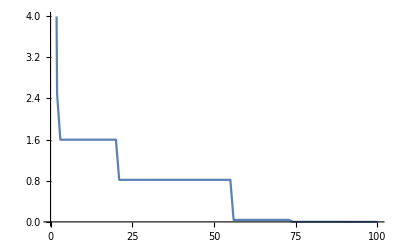

```mathematica
ListLinePlot[fitCurve]
```

```mathematica
DSolve
```